Finite Friction Model
(todo: non-dimensionalize the distance moved?)

what happens if μ is not infinite?
Set the horizontal boundary at y = d, particle 1 starts in contact with the boundary at (0,d), particle 2 starts at (0,0).  Initial separation is d.
We command a move of length1 at angle θ  (Sin[θ] must be < d).
particle 2 ends at (Cos[θ],Sin[θ])
particle 1 ends at (Cos[θ]- Friction,d)
Friction = Min[Cos[θ],μSin[θ]]
particle 1 ends at (Cos[θ]- Friction,d).

Simple calculations show that the θ to maximize the separation distance is always the Cot^-1(μ). This value will increase the separation distance if d< 1/2 (1+μ^2) Sin[θ].
This means the separation distance will increase if d<1/2 √(1+μ^2) and Sin[θ] <d
However, we move up Sin[θ]
Sin[θ]<d<1/2 √(1+μ^2)
Sin[ArcCot[μ]]<d<1/2 √(1+μ^2)
1/(√(μ^2+1))<d<1/2 √(1+μ^2)
I want to know combinations of θ, μ, d that increase the total separation.

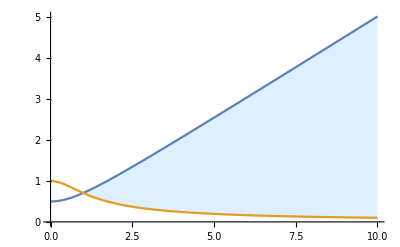

```mathematica
Plot[{1/2 √(1+μ^2),1/(√(μ^2+1))},{μ,0,10},Filling->{1->{{2},{None,LightBlue}}}]
```

```mathematica
Sin[ArcCot[μ]]
```

```mathematica
1/(√(μ^2+1))
```

```mathematica
ArcCot[0]
```

π/2

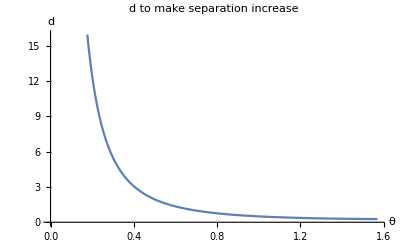

```mathematica
Plot[1/2 (1+Cot[θ]^2) Sin[ArcCot[θ]],{θ,0,π/2},AxesLabel->{"θ","d"},PlotLabel->"d to make separation increase"]
```

```mathematica
FullSimplify[Assuming[μ>0&&μ∈Reals, Sin[ArcCot[μ]]]]
```

1/(√(1+1/μ^2) μ)

```mathematica
1/(√(μ+1))
```

```mathematica
FullSimplify[(1+μ^2)1/(√(μ^2+1))]
```

√(1+μ^2)

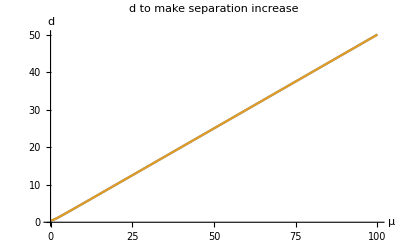

```mathematica
Plot[{1/2 (1+μ^2)1/(√(μ^2+1)),1/2 √(1+μ^2)},{μ,0,100},AxesLabel->{"μ","d"},PlotLabel->"d to make separation increase"]
```

```mathematica
Clear[d]
√((μ Sin[θ])^2+(d-Sin[θ])^2)≥ d
```

```mathematica
FullSimplify[Expand[(d-Sin[θ])^2+μ^2 Sin[θ]^2≥d^2]]
```

```mathematica
Solve[Sin[θ] (-2 d+(1+μ^2) Sin[θ])==0,d]
```

{{d→1/2 (1+μ^2) Sin[θ]}}

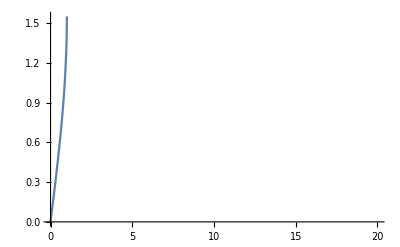

```mathematica
Plot[ArcSin[d],{d,0,20}]
```

```mathematica
Manipulate[
Module[{p1p,p2p},
p1p = {Cos[θ]-Min[Cos[θ],μ Sin[θ]],d};
p2p={Cos[θ], Sin[θ]};
If[Sin[θ]>d,θ = ArcSin[d]];
Graphics[{PointSize-> Large,
Brown,Rectangle[{-4,d},{4,d+4}],
Blue, {Opacity[0.5],Point[{0,d}]},Point[p1p],
Arrow[{{0,d},{Cos[θ],d}}],
Red, 
Arrow[{{Cos[θ],d+.02},p1p+{0,.02}}],
Arrow[{p1p,p1p+{0,-Sin[θ]}}],
 {Opacity[0.5],Point[{0,0}]},Point[p2p],
Black, Arrow[{{0,0},p2p}],
Brown, Arrow[{p1p,p2p}],Arrow[{p2p,p1p}],
Text[StringForm["   ``", Norm[ p1p-p2p]/d],1/2(p1p+p2p)]

},PlotRange->{{-.2,1.2},{-.2,d+.2}}]],
{d,0,10,Appearance->"Labeled"},
{θ,0,π/2,Appearance->"Labeled"},{μ,0,10,Appearance->"Labeled"}
]
```

```mathematica
Clear[d]
p1p = {Cos[θ]-Min[Cos[θ],μ Sin[θ]],d};
p2p={Cos[θ], Sin[θ]};
FullSimplify[Norm[ p1p-p2p]/d]
```

```mathematica
FullSimplify[(√((Min[Cos[θ],μ Sin[θ]])^2+(d-Sin[θ])^2))/d]
```

```mathematica
distanceRatio[μ_,θ_,d_]:=(√(Min[Cos[θ],μ Sin[θ]]^2+(d-Sin[θ])^2))/d
distanceRatio2[μ_,θ_,d_]:=If[Cot[θ]<μ,(√(1+d^2-2 d Sin[θ]))/d,(√((μ Sin[θ])^2+(d-Sin[θ])^2))/d]
```

```mathematica
distanceRatio2[μ_,θ_,d_]:=If[Cot[θ]<μ,(√(1+d^2-2 d Sin[θ]))/d,(√((μ Sin[θ])^2+(d-Sin[θ])^2))/d]
d= 2;Plot3D[{distanceRatio2[μ,θ,d],1},{θ,0,π/2},{μ,0,100},AxesLabel->{"θ","μ"},PlotRange->All,MaxRecursion->8]
```

-Graphics3D-

```mathematica
distance2[μ_,θ_,d_]:=If[Cot[θ]<μ,√(1+d^2-2 d Sin[θ]),√((μ Sin[θ])^2+(d-Sin[θ])^2)]
d=1;Plot3D[{distance2[μ,θ,d]-d,0},{θ,0,π/2},{μ,0,100},AxesLabel->{"θ","μ"},PlotRange->All,MaxRecursion->8]
```

-Graphics3D-

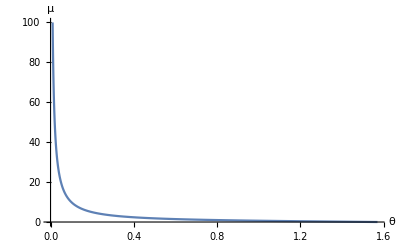

```mathematica
Plot[Cot[θ],{θ,0,π/2},AxesLabel->{"θ","μ"},PlotRange->{{0,π/2},{0,100}},MaxRecursion->8]
```

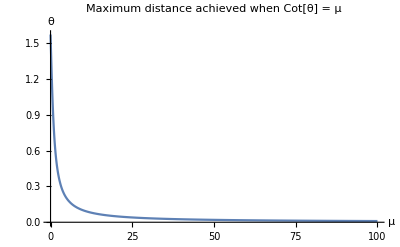

```mathematica
Plot[ArcCot[μ],{μ,0,100},AxesLabel->{"μ","θ"},PlotRange->{{0,100},{0,π/2}},MaxRecursion->8,PlotLabel->"Maximum distance achieved when Cot[θ] = μ"]
```

```mathematica
d= 1;Plot3D[{(√(Min[Cos[θ],μ Sin[θ]]^2+(d-Sin[θ])^2))/d,d},{θ,0,π/2},{μ,0,100},AxesLabel->{"θ","μ"},PlotRange->All,Exclusions->None,MaxRecursion->8]
```

-Graphics3D-

```mathematica
d= 1;Plot3D[{(√(Min[Cos[θ],μ Sin[θ]]^2+(d-Sin[θ])^2))/d},{θ,0,π/2},{μ,0,100},AxesLabel->{"θ","μ"},PlotRange->All,ExclusionsStyle->{Opacity[0.5],Directive[Thick,Blue]},MaxRecursion->5,Mesh->All]
```

-Graphics3D-

```mathematica
FullSimplify[(Cos[θ]-(Cos[θ]-Min[Cos[θ],μ Sin[θ]]))^2]
```

Min[Cos[θ],μ Sin[θ]]^2

```mathematica
d=1;
Plot3D[{√((d-Sin[θ])^2+Min[Cos[θ],μ Sin[θ]]^2),0},{θ,0,π/2},{μ,0,100},AxesLabel->{"θ","μ"},PlotRange->All]
```

-Graphics3D-

```mathematica
d=1;
Plot3D[{√((d-Sin[θ])^2+Min[Cos[θ],μ Sin[θ]]^2)-d,0},{θ,0,π/2},{μ,0,100},AxesLabel->{"θ","μ"},PlotRange->All]
```

-Graphics3D-

### The coefficient of friction depends on the objects that are causing friction. The value is usually between 0 and 1 but can be greater than 1. A value of 0 means there is no friction at all between the objects. This is only theoretically possible. All objects in the real world will have some friction when they touch each other. A value of 1 means the frictional force is equal to the normal force. Some people think that the coefficient of friction can never be more than 1, but this is not true. A coefficient of friction that is more than one just means that friction is stronger than the normal force. An object such as silicone rubber, for example, can have a coefficient of friction much greater than one. The coefficient of friction can also be changed by the mass and speed of the moving object.